```mathematica
pivots[A_]:=Flatten[FirstPosition[1]/@Transpose[A]]
```

```mathematica
pMatrix[n_]:=Table[
Which[i==2&&j==1||i==1&&j==2,-1/2,
i==j&&i>2,1,
True,0],{i, n},{j,n}]
```

```mathematica
gramMatrix[W_]:=Simplify[Transpose[W].pMatrix[Length[W]].W]
```

```mathematica
linearRelationsMatrix[G_]:=RowReduce[G][[1;;MatrixRank[G]]]//Transpose
```

```mathematica
linearRelations[L_]:=Select[
Table[Equal[Subscript[b, i],L[[i]].Table[Subscript[b, i],{i,pivots[L]}]],{i,Length[L]}],Not[BooleanQ[#]]&]
```

```mathematica
linearRelationsFromW=linearRelations@*linearRelationsMatrix@*gramMatrix;
```

```mathematica
inverseLinearRelations[G_]:=Table[If[i==#,1,0],{i,Length[G[[1]]]}]&/@Flatten[FirstPosition[#,1]&/@(RowReduce[G]//Select[Not[AllTrue[#,#==0&]]&])]
```

```mathematica
quadraticFormMatrix[G_,L_]:=Inverse[Table[G[[i, j]],{i,pivots[L]},{j,pivots[L]}]]
```

```mathematica
quadraticForm[Q_,L_]:=Module[{v=Table[Subscript[b, i],{i,pivots[L]}]},Simplify[v.Q.v==0]]
```

```mathematica
quadform[W_]:=Module[{G=gramMatrix[W]},Module[{L=linearRelationsMatrix[G]},quadraticForm[quadraticFormMatrix[G,L],L]]]
```

```mathematica
quadformFromG[G_]:=Module[{L=linearRelationsMatrix[G]},quadraticForm[quadraticFormMatrix[G,L],L]]
```

```mathematica
graphFromG[G_]:=PlanarGraph[AdjacencyGraph[If[#==-1,1,0]&/@#&/@G,VertexLabels->"Name"]]
```

```mathematica
nextCandidate[s_,t_,adj_]:=Block[{length,pos},length=Length[adj];
pos=Mod[Position[adj,s][[1,1]]+1,length,1];
{t,adj[[pos]]}];
```

```mathematica
FindFace[g_?PlanarGraphQ]:=Block[{emb},emb=GraphEmbedding[g,"PlanarEmbedding"];
FindFace[g,emb]];

FindFace[g_?PlanarGraphQ,emb_]:=Block[{m,orderings,pAdj,rightF,s,t,initial,face},m=AdjacencyMatrix[g];
Table[pAdj[v]=SortBy[Pick[VertexList[g],m[[v]],1],ArcTan@@(emb[[v]]-emb[[#]])&],{v,VertexList[g]}];
rightF[_]:=False;
Reap[Table[If[!rightF[e],s=e[[1]];
t=e[[2]];
initial=s;
face={s};
While[t=!=initial,rightF[UndirectedEdge[s,t]]=True;
{s,t}=nextCandidate[s,t,pAdj[t]];
face=Join[face,{s}];];
Sow[face];],{e,EdgeList[g]}]][[2,1]]]
```

```mathematica
findGenerators[faces_,vertices_,G_]:=Table[Block[{face,otherVertex,verticesOnFace,allVertices,Gp,P,Gnew,L,Q,Qform,sol1,sol2,sols,coeff,coeffTable,small,Li,P2},
face=faces[[i]];
verticesOnFace=Sort[RandomSample[face,3]];
otherVertex=RandomChoice[Select[vertices,Not[MemberQ[face,#]]&]];
allVertices=Append[verticesOnFace,otherVertex];
P=Transpose[IdentityMatrix[Length[vertices]][[#]]&/@DeleteDuplicates[Join[allVertices,vertices]]];
Gnew=Transpose[P].G.P;
L=linearRelationsMatrix[Gnew];
Gp=Table[G[[i,j]],{i,allVertices},{j,allVertices}];
Q=Inverse[Gp];
Qform=(#.Q.#&[Table[Subscript[b, j],{j,allVertices}]])==0;
sols=Expand[FullSimplify[Total[#[[1]][[2]]&/@Solve[Qform,Subscript[b, otherVertex]]]]];
coeff=Table[sols/.Table[Subscript[b, i]->If[i==curr,1,0],{i,allVertices}],{curr,allVertices}];
small=IdentityMatrix[Length[allVertices]];
small[[-1]]=Table[If[j==4,-1,If[MemberQ[verticesOnFace,allVertices[[j]]],coeff[[j]],0]],{j,Length[allVertices]}];
Li=Table[Table[If[j==k,1,0],{j,Length[vertices]}],{k,allVertices}];
P2=Table[If[j==k,1,0],{j,Length[vertices]},{k,DeleteDuplicates[Join[allVertices,vertices]]}];
P2.L.small.Li
],{i,Length[faces]}]
```

```mathematica
findGeneratorsN[faces_,vertices_,G_]:=Table[Block[{face,otherVertex,verticesOnFace,allVertices,Gp,P,Gnew,L,Q,Qform,sol1,sol2,sols,coeff,coeffTable,small,Li,P2},
face=faces[[i]];
verticesOnFace=Sort[RandomSample[face,3]];
otherVertex=RandomChoice[Select[vertices,Not[MemberQ[face,#]]&]];
allVertices=Append[verticesOnFace,otherVertex];
P=Transpose[IdentityMatrix[Length[vertices]][[#]]&/@DeleteDuplicates[Join[allVertices,vertices]]];
Gnew=Transpose[P].G.P;
L=linearRelationsMatrix[Gnew];
Gp=Table[G[[i,j]],{i,allVertices},{j,allVertices}];
Q=Inverse[Gp];
Qform=(#.Q.#&[Table[Subscript[b, j],{j,allVertices}]])==0;
sols=Expand[FullSimplify[Total[#[[1]][[2]]&/@NSolve[Qform,Subscript[b, otherVertex]]]]];
coeff=Table[sols/.Table[Subscript[b, i]->If[i==curr,1,0],{i,allVertices}],{curr,allVertices}];
small=IdentityMatrix[Length[allVertices]];
small[[-1]]=Table[If[j==4,-1,If[MemberQ[verticesOnFace,allVertices[[j]]],coeff[[j]],0]],{j,Length[allVertices]}];
Li=Table[Table[If[j==k,1,0],{j,Length[vertices]}],{k,allVertices}];
P2=Table[If[j==k,1,0],{j,Length[vertices]},{k,DeleteDuplicates[Join[allVertices,vertices]]}];
P2.L.small.Li
],{i,Length[faces]}]
```

```mathematica
findGeneratorsFromG[G_]:=findGeneratorsN[FindFace[PlanarGraph[AdjacencyGraph[If[#==-1,1,0]&/@#&/@G,VertexLabels->"Name"]]],Range[Length[G]],G]
```

```mathematica
search[generators_,current_,lastgen_,upperBound_,faces_]:=Block[{totals,invalid},
invalid[σ_,face_]:=σ==lastgen||AllTrue[Delete[σ.current,{#}&/@face],#>upperBound&];
totals[i_]:=If[invalid[generators⟦i⟧,faces⟦i⟧],0,
Length[current]-Length[faces⟦i⟧]-Length[Select[Delete[current,{#}&/@faces⟦i⟧],#>upperBound&]]+search[generators,generators⟦i⟧.current,generators⟦i⟧,upperBound,faces]];
Total[totals/@Range[Length[generators]]]]
```

```mathematica
$RecursionLimit=16384
```

16384

```mathematica
fractalDimensionFromG[G_,max_,delta_,root_]:=Block[{xs,ys,data,graph,faces,sigmas,nlm,params},
xs=Range[delta,max,delta];
graph=graphFromG[G];
faces=FindFace[graph];
sigmas=findGeneratorsFromG[G];
ys=search[sigmas,root,{},#,faces]+Length[root]&/@xs;
data={xs⟦#⟧,ys⟦#⟧}&/@Range[Length[ys]];
nlm=NonlinearModelFit[data,a x^b,{a,b},x];
params=nlm["BestFitParameters"];
Print[nlm["RSquared"]];
b/.params
]
```

```mathematica
pyramidG[n_]:=Table[Which[i==0&&j==0,1,i==0||j==0,-1,True,1-(2 Sin[(Abs[i-j]π)/n]^2)/Sin[π/n]^2],{i,0,n},{j,0,n}]
```

```mathematica
pyramidG[5]//Simplify//MatrixForm
```

(1 | -1 | -1 | -1 | -1 | -1
-1 | 1 | -1 | -2-√5 | -2-√5 | -1
-1 | -1 | 1 | -1 | -2-√5 | -2-√5
-1 | -2-√5 | -1 | 1 | -1 | -2-√5
-1 | -2-√5 | -2-√5 | -1 | 1 | -1
-1 | -1 | -2-√5 | -2-√5 | -1 | 1)

```mathematica
pyramidFractalDimension[n_,max_,delta_]:=fractalDimensionFromG[N[pyramidG[n]],max,delta,N[Table[If[i==n+1,-1,(Sec[π/n]+Tan[π/n])/Tan[π/n]],{i,n+1}]]]
```

```mathematica
G={{1,-8-3 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),3 (-2-Sqrt[5]),-2-Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],3 (-2-Sqrt[5]),-1,-1,-1,-5-2 Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5]},{-8-3 Sqrt[5],1,-5-2 Sqrt[5],-5-2 Sqrt[5],-1,-1,-5-2 Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],-1,3 (-2-Sqrt[5]),3 (-2-Sqrt[5]),3 (-2-Sqrt[5]),-2-Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],-2-Sqrt[5]},{-2-Sqrt[5],-5-2 Sqrt[5],1,3 (-2-Sqrt[5]),-2-Sqrt[5],3 (-2-Sqrt[5]),-1,-5-2 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-1,-5-2 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),-1,-8-3 Sqrt[5]},{-2-Sqrt[5],-5-2 Sqrt[5],3 (-2-Sqrt[5]),1,3 (-2-Sqrt[5]),-2-Sqrt[5],-5-2 Sqrt[5],-1,-5-2 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-1,-2-Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5],-8-3 Sqrt[5],-1},{3 (-2-Sqrt[5]),-1,-2-Sqrt[5],3 (-2-Sqrt[5]),1,-2-Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],3 (-2-Sqrt[5]),-1,-2-Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-8-3 Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-1,-5-2 Sqrt[5]},{3 (-2-Sqrt[5]),-1,3 (-2-Sqrt[5]),-2-Sqrt[5],-2-Sqrt[5],1,-5-2 Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),-5-2 Sqrt[5],-2-Sqrt[5],-1,-2-Sqrt[5],-8-3 Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-1},{-2-Sqrt[5],-5-2 Sqrt[5],-1,-5-2 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],1,-2-Sqrt[5],-5-2 Sqrt[5],3 (-2-Sqrt[5]),-1,-2-Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5],-5-2 Sqrt[5],-1,-5-2 Sqrt[5],-8-3 Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5])},{-2-Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-1,-5-2 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],1,3 (-2-Sqrt[5]),-5-2 Sqrt[5],-2-Sqrt[5],-1,3 (-2-Sqrt[5]),-5-2 Sqrt[5],-2-Sqrt[5],-1,-8-3 Sqrt[5],-5-2 Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5]},{-2-Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],3 (-2-Sqrt[5]),-5-2 Sqrt[5],3 (-2-Sqrt[5]),1,-1,3 (-2-Sqrt[5]),-8-3 Sqrt[5],-2-Sqrt[5],-1,-2-Sqrt[5],-5-2 Sqrt[5],-1,-2-Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5]},{-2-Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),-5-2 Sqrt[5],3 (-2-Sqrt[5]),-5-2 Sqrt[5],-1,1,-8-3 Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5],-2-Sqrt[5],-1,-5-2 Sqrt[5],-2-Sqrt[5],-1,-5-2 Sqrt[5],-2-Sqrt[5]},{-5-2 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-1,-2-Sqrt[5],-1,-2-Sqrt[5],3 (-2-Sqrt[5]),-8-3 Sqrt[5],1,-1,-5-2 Sqrt[5],-5-2 Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5],-5-2 Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5],-5-2 Sqrt[5]},{-5-2 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],-1,-2-Sqrt[5],-1,-8-3 Sqrt[5],3 (-2-Sqrt[5]),-1,1,-5-2 Sqrt[5],3 (-2-Sqrt[5]),-5-2 Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),-5-2 Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5]},{3 (-2-Sqrt[5]),-1,-5-2 Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),3 (-2-Sqrt[5]),-2-Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],1,-5-2 Sqrt[5],-5-2 Sqrt[5],-8-3 Sqrt[5],-1,-1,-2-Sqrt[5],-2-Sqrt[5]},{-1,3 (-2-Sqrt[5]),-1,-5-2 Sqrt[5],-5-2 Sqrt[5],-8-3 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-1,-2-Sqrt[5],-5-2 Sqrt[5],3 (-2-Sqrt[5]),-5-2 Sqrt[5],1,-2-Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5])},{-1,3 (-2-Sqrt[5]),-5-2 Sqrt[5],-1,-8-3 Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],-1,3 (-2-Sqrt[5]),-5-2 Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],1,-2-Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5]},{-1,3 (-2-Sqrt[5]),-2-Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-1,-1,-5-2 Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],-8-3 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],1,3 (-2-Sqrt[5]),3 (-2-Sqrt[5]),-5-2 Sqrt[5],-5-2 Sqrt[5]},{-5-2 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-8-3 Sqrt[5],-1,-2-Sqrt[5],-5-2 Sqrt[5],3 (-2-Sqrt[5]),-1,-2-Sqrt[5],-5-2 Sqrt[5],3 (-2-Sqrt[5]),1,-2-Sqrt[5],-1,-5-2 Sqrt[5]},{-5-2 Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-8-3 Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-1,3 (-2-Sqrt[5]),-5-2 Sqrt[5],-1,-5-2 Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5],1,-5-2 Sqrt[5],-1},{-5-2 Sqrt[5],-2-Sqrt[5],-1,-8-3 Sqrt[5],-1,-5-2 Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),-5-2 Sqrt[5],-1,-5-2 Sqrt[5],1,3 (-2-Sqrt[5])},{-5-2 Sqrt[5],-2-Sqrt[5],-8-3 Sqrt[5],-1,-5-2 Sqrt[5],-1,3 (-2-Sqrt[5]),-2-Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-1,3 (-2-Sqrt[5]),1}}
```

{{1,-8-3 √5,-2-√5,-2-√5,3 (-2-√5),3 (-2-√5),-2-√5,-2-√5,-2-√5,-2-√5,-5-2 √5,-5-2 √5,3 (-2-√5),-1,-1,-1,-5-2 √5,-5-2 √5,-5-2 √5,-5-2 √5},{-8-3 √5,1,-5-2 √5,-5-2 √5,-1,-1,-5-2 √5,-5-2 √5,-5-2 √5,-5-2 √5,-2-√5,-2-√5,-1,3 (-2-√5),3 (-2-√5),3 (-2-√5),-2-√5,-2-√5,-2-√5,-2-√5},{-2-√5,-5-2 √5,1,3 (-2-√5),-2-√5,3 (-2-√5),-1,-5-2 √5,-2-√5,-5-2 √5,-2-√5,-5-2 √5,-5-2 √5,-1,-5-2 √5,-2-√5,-2-√5,3 (-2-√5),-1,-8-3 √5},{-2-√5,-5-2 √5,3 (-2-√5),1,3 (-2-√5),-2-√5,-5-2 √5,-1,-5-2 √5,-2-√5,-5-2 √5,-2-√5,-5-2 √5,-5-2 √5,-1,-2-√5,3 (-2-√5),-2-√5,-8-3 √5,-1},{3 (-2-√5),-1,-2-√5,3 (-2-√5),1,-2-√5,-2-√5,-5-2 √5,-5-2 √5,3 (-2-√5),-1,-2-√5,-2-√5,-5-2 √5,-8-3 √5,-5-2 √5,-2-√5,-5-2 √5,-1,-5-2 √5},{3 (-2-√5),-1,3 (-2-√5),-2-√5,-2-√5,1,-5-2 √5,-2-√5,3 (-2-√5),-5-2 √5,-2-√5,-1,-2-√5,-8-3 √5,-5-2 √5,-5-2 √5,-5-2 √5,-2-√5,-5-2 √5,-1},{-2-√5,-5-2 √5,-1,-5-2 √5,-2-√5,-5-2 √5,1,-2-√5,-5-2 √5,3 (-2-√5),-1,-2-√5,3 (-2-√5),-2-√5,-5-2 √5,-1,-5-2 √5,-8-3 √5,-2-√5,3 (-2-√5)},{-2-√5,-5-2 √5,-5-2 √5,-1,-5-2 √5,-2-√5,-2-√5,1,3 (-2-√5),-5-2 √5,-2-√5,-1,3 (-2-√5),-5-2 √5,-2-√5,-1,-8-3 √5,-5-2 √5,3 (-2-√5),-2-√5},{-2-√5,-5-2 √5,-2-√5,-5-2 √5,-5-2 √5,3 (-2-√5),-5-2 √5,3 (-2-√5),1,-1,3 (-2-√5),-8-3 √5,-2-√5,-1,-2-√5,-5-2 √5,-1,-2-√5,-2-√5,-5-2 √5},{-2-√5,-5-2 √5,-5-2 √5,-2-√5,3 (-2-√5),-5-2 √5,3 (-2-√5),-5-2 √5,-1,1,-8-3 √5,3 (-2-√5),-2-√5,-2-√5,-1,-5-2 √5,-2-√5,-1,-5-2 √5,-2-√5},{-5-2 √5,-2-√5,-2-√5,-5-2 √5,-1,-2-√5,-1,-2-√5,3 (-2-√5),-8-3 √5,1,-1,-5-2 √5,-5-2 √5,3 (-2-√5),-2-√5,-5-2 √5,3 (-2-√5),-2-√5,-5-2 √5},{-5-2 √5,-2-√5,-5-2 √5,-2-√5,-2-√5,-1,-2-√5,-1,-8-3 √5,3 (-2-√5),-1,1,-5-2 √5,3 (-2-√5),-5-2 √5,-2-√5,3 (-2-√5),-5-2 √5,-5-2 √5,-2-√5},{3 (-2-√5),-1,-5-2 √5,-5-2 √5,-2-√5,-2-√5,3 (-2-√5),3 (-2-√5),-2-√5,-2-√5,-5-2 √5,-5-2 √5,1,-5-2 √5,-5-2 √5,-8-3 √5,-1,-1,-2-√5,-2-√5},{-1,3 (-2-√5),-1,-5-2 √5,-5-2 √5,-8-3 √5,-2-√5,-5-2 √5,-1,-2-√5,-5-2 √5,3 (-2-√5),-5-2 √5,1,-2-√5,-2-√5,-2-√5,-5-2 √5,-2-√5,3 (-2-√5)},{-1,3 (-2-√5),-5-2 √5,-1,-8-3 √5,-5-2 √5,-5-2 √5,-2-√5,-2-√5,-1,3 (-2-√5),-5-2 √5,-5-2 √5,-2-√5,1,-2-√5,-5-2 √5,-2-√5,3 (-2-√5),-2-√5},{-1,3 (-2-√5),-2-√5,-2-√5,-5-2 √5,-5-2 √5,-1,-1,-5-2 √5,-5-2 √5,-2-√5,-2-√5,-8-3 √5,-2-√5,-2-√5,1,3 (-2-√5),3 (-2-√5),-5-2 √5,-5-2 √5},{-5-2 √5,-2-√5,-2-√5,3 (-2-√5),-2-√5,-5-2 √5,-5-2 √5,-8-3 √5,-1,-2-√5,-5-2 √5,3 (-2-√5),-1,-2-√5,-5-2 √5,3 (-2-√5),1,-2-√5,-1,-5-2 √5},{-5-2 √5,-2-√5,3 (-2-√5),-2-√5,-5-2 √5,-2-√5,-8-3 √5,-5-2 √5,-2-√5,-1,3 (-2-√5),-5-2 √5,-1,-5-2 √5,-2-√5,3 (-2-√5),-2-√5,1,-5-2 √5,-1},{-5-2 √5,-2-√5,-1,-8-3 √5,-1,-5-2 √5,-2-√5,3 (-2-√5),-2-√5,-5-2 √5,-2-√5,-5-2 √5,-2-√5,-2-√5,3 (-2-√5),-5-2 √5,-1,-5-2 √5,1,3 (-2-√5)},{-5-2 √5,-2-√5,-8-3 √5,-1,-5-2 √5,-1,3 (-2-√5),-2-√5,-5-2 √5,-2-√5,-5-2 √5,-2-√5,-2-√5,3 (-2-√5),-2-√5,-5-2 √5,-5-2 √5,-1,3 (-2-√5),1}}

```mathematica
(*fractalDimensionFromG[G,1000,20,{-1,2,2,4,4,7}]*)
```

```mathematica
faces-1
```

-1+faces

```mathematica
faces=FindFace[PlanarGraph[AdjacencyGraph[If[#==-1,1,0]&/@#&/@G,VertexLabels->"Name"]]]
```

{{1,14,9,10,15},{1,15,4,8,16},{1,16,7,3,14},{2,5,11,12,6},{2,6,20,18,13},{2,13,17,19,5},{3,7,11,5,19},{3,19,17,9,14},{4,15,10,18,20},{4,20,6,12,8},{7,16,8,12,11},{9,17,13,18,10}}

```mathematica
(*sigmas=findGeneratorsFromG[G]*)
```

```mathematica
(*Timing[pyramidFractalDimension[11,100000,10000]]*)
```

```mathematica
G={{1,-8-3 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),3 (-2-Sqrt[5]),-2-Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],3 (-2-Sqrt[5]),-1,-1,-1,-5-2 Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5]},{-8-3 Sqrt[5],1,-5-2 Sqrt[5],-5-2 Sqrt[5],-1,-1,-5-2 Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],-1,3 (-2-Sqrt[5]),3 (-2-Sqrt[5]),3 (-2-Sqrt[5]),-2-Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],-2-Sqrt[5]},{-2-Sqrt[5],-5-2 Sqrt[5],1,3 (-2-Sqrt[5]),-2-Sqrt[5],3 (-2-Sqrt[5]),-1,-5-2 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-1,-5-2 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),-1,-8-3 Sqrt[5]},{-2-Sqrt[5],-5-2 Sqrt[5],3 (-2-Sqrt[5]),1,3 (-2-Sqrt[5]),-2-Sqrt[5],-5-2 Sqrt[5],-1,-5-2 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-1,-2-Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5],-8-3 Sqrt[5],-1},{3 (-2-Sqrt[5]),-1,-2-Sqrt[5],3 (-2-Sqrt[5]),1,-2-Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],3 (-2-Sqrt[5]),-1,-2-Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-8-3 Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-1,-5-2 Sqrt[5]},{3 (-2-Sqrt[5]),-1,3 (-2-Sqrt[5]),-2-Sqrt[5],-2-Sqrt[5],1,-5-2 Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),-5-2 Sqrt[5],-2-Sqrt[5],-1,-2-Sqrt[5],-8-3 Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-1},{-2-Sqrt[5],-5-2 Sqrt[5],-1,-5-2 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],1,-2-Sqrt[5],-5-2 Sqrt[5],3 (-2-Sqrt[5]),-1,-2-Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5],-5-2 Sqrt[5],-1,-5-2 Sqrt[5],-8-3 Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5])},{-2-Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-1,-5-2 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],1,3 (-2-Sqrt[5]),-5-2 Sqrt[5],-2-Sqrt[5],-1,3 (-2-Sqrt[5]),-5-2 Sqrt[5],-2-Sqrt[5],-1,-8-3 Sqrt[5],-5-2 Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5]},{-2-Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],3 (-2-Sqrt[5]),-5-2 Sqrt[5],3 (-2-Sqrt[5]),1,-1,3 (-2-Sqrt[5]),-8-3 Sqrt[5],-2-Sqrt[5],-1,-2-Sqrt[5],-5-2 Sqrt[5],-1,-2-Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5]},{-2-Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),-5-2 Sqrt[5],3 (-2-Sqrt[5]),-5-2 Sqrt[5],-1,1,-8-3 Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5],-2-Sqrt[5],-1,-5-2 Sqrt[5],-2-Sqrt[5],-1,-5-2 Sqrt[5],-2-Sqrt[5]},{-5-2 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-1,-2-Sqrt[5],-1,-2-Sqrt[5],3 (-2-Sqrt[5]),-8-3 Sqrt[5],1,-1,-5-2 Sqrt[5],-5-2 Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5],-5-2 Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5],-5-2 Sqrt[5]},{-5-2 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],-1,-2-Sqrt[5],-1,-8-3 Sqrt[5],3 (-2-Sqrt[5]),-1,1,-5-2 Sqrt[5],3 (-2-Sqrt[5]),-5-2 Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),-5-2 Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5]},{3 (-2-Sqrt[5]),-1,-5-2 Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),3 (-2-Sqrt[5]),-2-Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],1,-5-2 Sqrt[5],-5-2 Sqrt[5],-8-3 Sqrt[5],-1,-1,-2-Sqrt[5],-2-Sqrt[5]},{-1,3 (-2-Sqrt[5]),-1,-5-2 Sqrt[5],-5-2 Sqrt[5],-8-3 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-1,-2-Sqrt[5],-5-2 Sqrt[5],3 (-2-Sqrt[5]),-5-2 Sqrt[5],1,-2-Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5])},{-1,3 (-2-Sqrt[5]),-5-2 Sqrt[5],-1,-8-3 Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],-1,3 (-2-Sqrt[5]),-5-2 Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],1,-2-Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5]},{-1,3 (-2-Sqrt[5]),-2-Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-1,-1,-5-2 Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],-8-3 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],1,3 (-2-Sqrt[5]),3 (-2-Sqrt[5]),-5-2 Sqrt[5],-5-2 Sqrt[5]},{-5-2 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-8-3 Sqrt[5],-1,-2-Sqrt[5],-5-2 Sqrt[5],3 (-2-Sqrt[5]),-1,-2-Sqrt[5],-5-2 Sqrt[5],3 (-2-Sqrt[5]),1,-2-Sqrt[5],-1,-5-2 Sqrt[5]},{-5-2 Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-8-3 Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-1,3 (-2-Sqrt[5]),-5-2 Sqrt[5],-1,-5-2 Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5],1,-5-2 Sqrt[5],-1},{-5-2 Sqrt[5],-2-Sqrt[5],-1,-8-3 Sqrt[5],-1,-5-2 Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),-5-2 Sqrt[5],-1,-5-2 Sqrt[5],1,3 (-2-Sqrt[5])},{-5-2 Sqrt[5],-2-Sqrt[5],-8-3 Sqrt[5],-1,-5-2 Sqrt[5],-1,3 (-2-Sqrt[5]),-2-Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-1,3 (-2-Sqrt[5]),1}}
```

{{1,-8-3 √5,-2-√5,-2-√5,3 (-2-√5),3 (-2-√5),-2-√5,-2-√5,-2-√5,-2-√5,-5-2 √5,-5-2 √5,3 (-2-√5),-1,-1,-1,-5-2 √5,-5-2 √5,-5-2 √5,-5-2 √5},{-8-3 √5,1,-5-2 √5,-5-2 √5,-1,-1,-5-2 √5,-5-2 √5,-5-2 √5,-5-2 √5,-2-√5,-2-√5,-1,3 (-2-√5),3 (-2-√5),3 (-2-√5),-2-√5,-2-√5,-2-√5,-2-√5},{-2-√5,-5-2 √5,1,3 (-2-√5),-2-√5,3 (-2-√5),-1,-5-2 √5,-2-√5,-5-2 √5,-2-√5,-5-2 √5,-5-2 √5,-1,-5-2 √5,-2-√5,-2-√5,3 (-2-√5),-1,-8-3 √5},{-2-√5,-5-2 √5,3 (-2-√5),1,3 (-2-√5),-2-√5,-5-2 √5,-1,-5-2 √5,-2-√5,-5-2 √5,-2-√5,-5-2 √5,-5-2 √5,-1,-2-√5,3 (-2-√5),-2-√5,-8-3 √5,-1},{3 (-2-√5),-1,-2-√5,3 (-2-√5),1,-2-√5,-2-√5,-5-2 √5,-5-2 √5,3 (-2-√5),-1,-2-√5,-2-√5,-5-2 √5,-8-3 √5,-5-2 √5,-2-√5,-5-2 √5,-1,-5-2 √5},{3 (-2-√5),-1,3 (-2-√5),-2-√5,-2-√5,1,-5-2 √5,-2-√5,3 (-2-√5),-5-2 √5,-2-√5,-1,-2-√5,-8-3 √5,-5-2 √5,-5-2 √5,-5-2 √5,-2-√5,-5-2 √5,-1},{-2-√5,-5-2 √5,-1,-5-2 √5,-2-√5,-5-2 √5,1,-2-√5,-5-2 √5,3 (-2-√5),-1,-2-√5,3 (-2-√5),-2-√5,-5-2 √5,-1,-5-2 √5,-8-3 √5,-2-√5,3 (-2-√5)},{-2-√5,-5-2 √5,-5-2 √5,-1,-5-2 √5,-2-√5,-2-√5,1,3 (-2-√5),-5-2 √5,-2-√5,-1,3 (-2-√5),-5-2 √5,-2-√5,-1,-8-3 √5,-5-2 √5,3 (-2-√5),-2-√5},{-2-√5,-5-2 √5,-2-√5,-5-2 √5,-5-2 √5,3 (-2-√5),-5-2 √5,3 (-2-√5),1,-1,3 (-2-√5),-8-3 √5,-2-√5,-1,-2-√5,-5-2 √5,-1,-2-√5,-2-√5,-5-2 √5},{-2-√5,-5-2 √5,-5-2 √5,-2-√5,3 (-2-√5),-5-2 √5,3 (-2-√5),-5-2 √5,-1,1,-8-3 √5,3 (-2-√5),-2-√5,-2-√5,-1,-5-2 √5,-2-√5,-1,-5-2 √5,-2-√5},{-5-2 √5,-2-√5,-2-√5,-5-2 √5,-1,-2-√5,-1,-2-√5,3 (-2-√5),-8-3 √5,1,-1,-5-2 √5,-5-2 √5,3 (-2-√5),-2-√5,-5-2 √5,3 (-2-√5),-2-√5,-5-2 √5},{-5-2 √5,-2-√5,-5-2 √5,-2-√5,-2-√5,-1,-2-√5,-1,-8-3 √5,3 (-2-√5),-1,1,-5-2 √5,3 (-2-√5),-5-2 √5,-2-√5,3 (-2-√5),-5-2 √5,-5-2 √5,-2-√5},{3 (-2-√5),-1,-5-2 √5,-5-2 √5,-2-√5,-2-√5,3 (-2-√5),3 (-2-√5),-2-√5,-2-√5,-5-2 √5,-5-2 √5,1,-5-2 √5,-5-2 √5,-8-3 √5,-1,-1,-2-√5,-2-√5},{-1,3 (-2-√5),-1,-5-2 √5,-5-2 √5,-8-3 √5,-2-√5,-5-2 √5,-1,-2-√5,-5-2 √5,3 (-2-√5),-5-2 √5,1,-2-√5,-2-√5,-2-√5,-5-2 √5,-2-√5,3 (-2-√5)},{-1,3 (-2-√5),-5-2 √5,-1,-8-3 √5,-5-2 √5,-5-2 √5,-2-√5,-2-√5,-1,3 (-2-√5),-5-2 √5,-5-2 √5,-2-√5,1,-2-√5,-5-2 √5,-2-√5,3 (-2-√5),-2-√5},{-1,3 (-2-√5),-2-√5,-2-√5,-5-2 √5,-5-2 √5,-1,-1,-5-2 √5,-5-2 √5,-2-√5,-2-√5,-8-3 √5,-2-√5,-2-√5,1,3 (-2-√5),3 (-2-√5),-5-2 √5,-5-2 √5},{-5-2 √5,-2-√5,-2-√5,3 (-2-√5),-2-√5,-5-2 √5,-5-2 √5,-8-3 √5,-1,-2-√5,-5-2 √5,3 (-2-√5),-1,-2-√5,-5-2 √5,3 (-2-√5),1,-2-√5,-1,-5-2 √5},{-5-2 √5,-2-√5,3 (-2-√5),-2-√5,-5-2 √5,-2-√5,-8-3 √5,-5-2 √5,-2-√5,-1,3 (-2-√5),-5-2 √5,-1,-5-2 √5,-2-√5,3 (-2-√5),-2-√5,1,-5-2 √5,-1},{-5-2 √5,-2-√5,-1,-8-3 √5,-1,-5-2 √5,-2-√5,3 (-2-√5),-2-√5,-5-2 √5,-2-√5,-5-2 √5,-2-√5,-2-√5,3 (-2-√5),-5-2 √5,-1,-5-2 √5,1,3 (-2-√5)},{-5-2 √5,-2-√5,-8-3 √5,-1,-5-2 √5,-1,3 (-2-√5),-2-√5,-5-2 √5,-2-√5,-5-2 √5,-2-√5,-2-√5,3 (-2-√5),-2-√5,-5-2 √5,-5-2 √5,-1,3 (-2-√5),1}}

```mathematica
root={1.6838616297871791,3.5522063477126107,0.5291610914079277,3.5522063477126107,1.6838616297871791,3.5522063477126107,-0.18448308813825243,1.6838616297871791,3.5522063477126107,4.706906886091862,0.5291610914079277,1.6838616297871791,4.706906886091862,1.6838616297871791,3.5522063477126107,0.5291610914079277,3.5522063477126107,5.420551065638042,1.6838616297871791,4.706906886091862};
```

```mathematica
(*fractalDimensionFromG[G,10000,100,root]*)
```

```mathematica
W={{0, 0, 0, -1}, {2, 0, 0, 1}, {0, 3, 0, 1}, {2, 3, √3, 2}};
```

```mathematica
P={{0, -1/2, 0, 0}, {-1/2, 0, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}};
```

```mathematica
G={{1, -1, -1, -2}, {-1, 1, -2, -1}, {-1, -2, 1, -1}, {-2, -1, -1, 1}};
```

```mathematica
W.P.Transpose[W]//MatrixForm
```

(1 | -1 | -1 | -2
-1 | 1 | -2 | -1
-1 | -2 | 1 | -1
-2 | -1 | -1 | 1)

```mathematica
v=Table[Subscript[b, i],{i,4}]
```

{b_1,b_2,b_3,b_4}

```mathematica
eq=Simplify[v.Inverse[G].v]==0
```

1/3 (b_1^2+b_2^2-2 b_1 (b_2+b_3)+(b_3-b_4)^2-2 b_2 b_4)==0

```mathematica
Total[Solve[eq,Subscript[b, 4]]/.{Subscript[b, 4]->x_}->x]
```

2 b_2+2 b_3

```mathematica
sigmas={
{{-1, 2, 2, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}},{{1, 0, 0, 0}, {2, -1, 0, 2}, {0, 0, 1, 0}, {0, 0, 0, 1}},{{1, 0, 0, 0}, {0, 1, 0, 0}, {2, 0, -1, 2}, {0, 0, 0, 1}},{{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 2, 2, -1}}
};
```

```mathematica
faces={{2,3,4},{1,3,4},{1,2,4},{1,2,3}};
```

```mathematica
root={-2,4,5,9};
```

```mathematica
Total[sigmas⟦1⟧.v]
```

-b_1+3 b_2+3 b_3+b_4

```mathematica
eq/.{Subscript[b, 1]->-2,Subscript[b, 2]->4,Subscript[b, 3]->5}//Simplify
```

b_4==9

```mathematica
(*search[sigmas,N[root],-1,20]*)
```

```mathematica
sigmas={
{{-1, 2, 2, 2}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}},{{1, 0, 0, 0}, {2, -1, 2, 2}, {0, 0, 1, 0}, {0, 0, 0, 1}},{{1, 0, 0, 0}, {0, 1, 0, 0}, {2, 2, -1, 2}, {0, 0, 0, 1}},{{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {2, 2, 2, -1}}
};
faces={{2,3,4},{1,3,4},{1,2,4},{1,2,3}};
root={-6,11,14,23};
Timing[search[sigmas,N[root],{},2000,faces]+Length[root]]
```

{0.036244,794}

```mathematica
G={{1, -1, -1, -1}, {-1, 1, -1, -1}, {-1, -1, 1, -1}, {-1, -1, -1, 1}}
```

{{1,-1,-1,-1},{-1,1,-1,-1},{-1,-1,1,-1},{-1,-1,-1,1}}

```mathematica
fractalDimensionFromG[G,1000,100,root]
```

0.999885

1.28525

```mathematica
sigmas⟦1⟧.root
```

{102,11,14,23}

```mathematica
sigmas⟦2⟧.sigmas⟦3⟧.sigmas⟦2⟧.root//Total
```

366

```mathematica
Total[root]
```

42

```mathematica
Total[sigmas⟦4⟧.sigmas⟦3⟧.sigmas⟦4⟧.root]
```

78

```mathematica
(*search[generators_,current_,lastgen_,upperBound_]:=
Total[Table[If[(generators⟦i⟧.current)⟦i⟧≥upperBound||Total[generators⟦i⟧.current]≤Total[current],0,1+search[generators,generators⟦i⟧.current,i,upperBound]],{i,4}]]*)
```

```mathematica
sigmas⟦3⟧.root
```

{-6,11,42,23}

```mathematica
(*search[sigmas,N[root],{},10,faces]*)
```

```mathematica
(*max=100;
delta=10;
xs=Range[1,max,delta];
ys=search[sigmas,N[root],-1,#]+Length[root]&/@xs;
data={xs⟦#⟧,ys⟦#⟧}&/@Range[Length[ys]];
nlm=NonlinearModelFit[data,a x^b,{a,b},x];
params=nlm["BestFitParameters"];
b/.params*)
```

```mathematica
nlm["RSquared"]
```

nlm[RSquared]

```mathematica
G=pyramidG[4]//Simplify
```

{{1,-1,-1,-1,-1},{-1,1,-1,-3,-1},{-1,-1,1,-1,-3},{-1,-3,-1,1,-1},{-1,-1,-3,-1,1}}

```mathematica
sigmas=findGeneratorsFromG[G]
```

{{{1.,0.,0.,0.,0.},{0.,1.,0.,0.,0.},{4.,4.,-1.,0.,2.},{4.,3.,-1.,0.,3.},{0.,0.,0.,0.,1.}},{{1.,0.,0.,0.,0.},{0.,1.,0.,0.,0.},{0.,0.,1.,0.,0.},{4.,2.,4.,-1.,0.},{4.,3.,3.,-1.,0.}},{{1.,0.,0.,0.,0.},{4.,-1.,4.,2.,0.},{0.,0.,1.,0.,0.},{0.,0.,0.,1.,0.},{4.,-1.,3.,3.,0.}},{{1.,0.,0.,0.,0.},{4.,0.,-1.,3.,3.},{4.,0.,-1.,4.,2.},{0.,0.,0.,1.,0.},{0.,0.,0.,0.,1.}},{{-1.,0.,1.,0.,1.},{0.,0.,1.,-1.,1.},{0.,0.,1.,0.,0.},{0.,0.,0.,1.,0.},{0.,0.,0.,0.,1.}}}

```mathematica
FindFace[graphFromG[G]]-1
```

{{0,1,4},{0,2,1},{0,3,2},{0,4,3},{1,2,3,4}}

```mathematica
root={-0.5131807550506294,1.2389279387920946,1.2389279387920946,1.2389279387920946,1.2389279387920946}
```

{-0.513181,1.23893,1.23893,1.23893,1.23893}

```mathematica
sigmas⟦1⟧.root
```

{-0.513181,1.23893,4.14192,4.14192,1.23893}

```mathematica
octahedron={{1, -1, -1, -1, -1, -3}, {-1, 1, -1, -3, -1, -1}, {-1, -1, 1, -1, -3, -1}, {-1, -3, -1, 1, -1, -1}, {-1, -1, -3, -1, 1, -1}, {-3, -1, -1, -1, -1, 1}}
```

{{1,-1,-1,-1,-1,-3},{-1,1,-1,-3,-1,-1},{-1,-1,1,-1,-3,-1},{-1,-3,-1,1,-1,-1},{-1,-1,-3,-1,1,-1},{-3,-1,-1,-1,-1,1}}

```mathematica
findGeneratorsFromG[octahedron]
```

{{{1.,0.,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.},{4.,4.,-1.,0.,2.,0.},{4.,3.,-1.,0.,3.,0.},{0.,0.,0.,0.,1.,0.},{3.,4.,-1.,0.,3.,0.}},{{1.,0.,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.},{0.,0.,1.,0.,0.,0.},{4.,3.,3.,0.,-1.,0.},{4.,4.,2.,0.,-1.,0.},{3.,4.,3.,0.,-1.,0.}},{{1.,0.,0.,0.,0.,0.},{4.,-1.,4.,2.,0.,0.},{0.,0.,1.,0.,0.,0.},{0.,0.,0.,1.,0.,0.},{4.,-1.,3.,3.,0.,0.},{3.,-1.,4.,3.,0.,0.}},{{1.,0.,0.,0.,0.,0.},{4.,-1.,0.,2.,4.,0.},{4.,-1.,0.,3.,3.,0.},{0.,0.,0.,1.,0.,0.},{0.,0.,0.,0.,1.,0.},{3.,-1.,0.,3.,4.,0.}},{{0.,3.,4.,-1.,0.,3.},{0.,1.,0.,0.,0.,0.},{0.,0.,1.,0.,0.,0.},{0.,2.,4.,-1.,0.,4.},{0.,3.,3.,-1.,0.,4.},{0.,0.,0.,0.,0.,1.}},{{0.,3.,0.,-1.,4.,3.},{0.,1.,0.,0.,0.,0.},{0.,3.,0.,-1.,3.,4.},{0.,2.,0.,-1.,4.,4.},{0.,0.,0.,0.,1.,0.},{0.,0.,0.,0.,0.,1.}},{{0.,-1.,4.,3.,0.,3.},{0.,-1.,4.,2.,0.,4.},{0.,0.,1.,0.,0.,0.},{0.,0.,0.,1.,0.,0.},{0.,-1.,3.,3.,0.,4.},{0.,0.,0.,0.,0.,1.}},{{-1.,0.,0.,4.,4.,2.},{-1.,0.,0.,3.,4.,3.},{-1.,0.,0.,4.,3.,3.},{0.,0.,0.,1.,0.,0.},{0.,0.,0.,0.,1.,0.},{0.,0.,0.,0.,0.,1.}}}

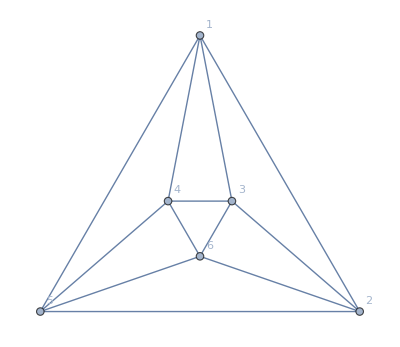

```mathematica
graphFromG[octahedron]
```

```mathematica
FindFace[graphFromG[octahedron]]-1
```

{{0,1,4},{0,2,1},{0,3,2},{0,4,3},{1,2,5},{1,5,4},{2,3,5},{3,4,5}}

```mathematica
penta=pyramidG[5]//Simplify
```

{{1,-1,-1,-1,-1,-1},{-1,1,-1,-2-√5,-2-√5,-1},{-1,-1,1,-1,-2-√5,-2-√5},{-1,-2-√5,-1,1,-1,-2-√5},{-1,-2-√5,-2-√5,-1,1,-1},{-1,-1,-2-√5,-2-√5,-1,1}}

```mathematica
faces=FindFace[graphFromG[penta]]
```

{{1,2,6},{1,3,2},{1,4,3},{1,5,4},{1,6,5},{2,3,4,5,6}}

```mathematica
sigmas=findGeneratorsFromG[penta]
```

{{{1.,0.,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.},{5.23607,4.23607,0.,-0.618034,0.,2.61803},{8.47214,5.23607,0.,-1.,0.,5.23607},{5.23607,2.61803,0.,-0.618034,0.,4.23607},{0.,0.,0.,0.,0.,1.}},{{1.,0.,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.},{0.,0.,1.,0.,0.,0.},{5.23607,3.61803,3.61803,0.,0.,-1.},{8.47214,6.8541,4.23607,0.,0.,-1.61803},{5.23607,5.23607,2.,0.,0.,-1.}},{{1.,0.,0.,0.,0.,0.},{5.23607,0.,4.23607,2.61803,0.,-0.618034},{0.,0.,1.,0.,0.,0.},{0.,0.,0.,1.,0.,0.},{5.23607,0.,2.61803,4.23607,0.,-0.618034},{8.47214,0.,5.23607,5.23607,0.,-1.}},{{1.,0.,0.,0.,0.,0.},{8.47214,-1.,0.,5.23607,5.23607,0.},{5.23607,-0.618034,0.,4.23607,2.61803,0.},{0.,0.,0.,1.,0.,0.},{0.,0.,0.,0.,1.,0.},{5.23607,-0.618034,0.,2.61803,4.23607,0.}},{{1.,0.,0.,0.,0.,0.},{5.23607,-1.,0.,0.,2.,5.23607},{8.47214,-1.61803,0.,0.,4.23607,6.8541},{5.23607,-1.,0.,0.,3.61803,3.61803},{0.,0.,0.,0.,1.,0.},{0.,0.,0.,0.,0.,1.}},{{-1.,0.763932,0.,0.,0.763932,-0.472136},{0.,1.,0.,0.,0.,0.},{0.,1.61803,0.,0.,1.,-1.61803},{0.,1.,0.,0.,1.61803,-1.61803},{0.,0.,0.,0.,1.,0.},{0.,0.,0.,0.,0.,1.}}}

```mathematica
root={-0.5511585907448705,1.4888455922394608,1.4888455922394608,1.4888455922394608,1.4888455922394608,1.4888455922394608};
```

```mathematica
Total[root]
```

6.89307

```mathematica
faces
```

{{1,2,6},{1,3,2},{1,4,3},{1,5,4},{1,6,5},{2,3,4,5,6}}

```mathematica
root
```

{-0.551159,1.48885,1.48885,1.48885,1.48885,1.48885}

```mathematica
sigmas⟦3⟧.sigmas⟦2⟧.sigmas⟦1⟧.root//Total
```

352.792

```mathematica
pyramidFractalDimension[5,1000,100]
```

0.999862

1.31685